# Spatial Curvature

## Γ = 1 and K = 1

```mathematica
mp1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

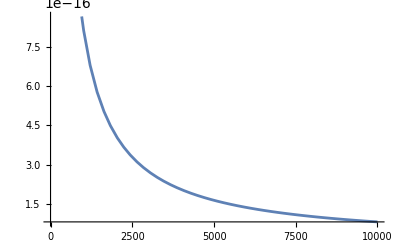

```mathematica
Plot[(2 mp1[r])/r^3+10^-52/3,{r,0,10000}]
```

## K = r and Γ = 1

```mathematica
mp2=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

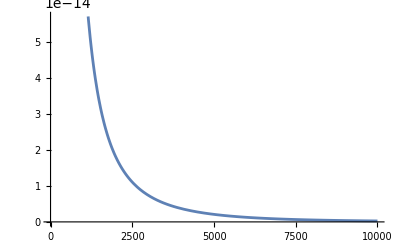

```mathematica
Plot[(2 mp2[r])/r^3+10^-52/3,{r,0,10000}]
```

## K = r/b and Γ = 1

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

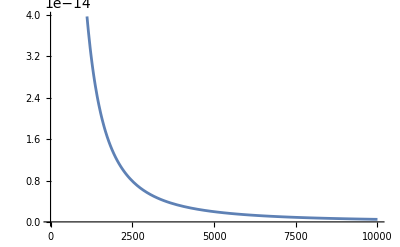

```mathematica
Plot[(2 mp3[r])/r^3+10^-52/3,{r,0,10000}]
```

## Combined Plots

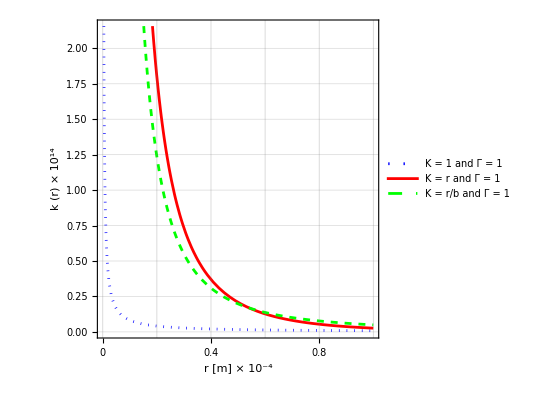

```mathematica
spatialcurv=Plot[{((2 mp1[r])/r^3+10^-52/3) 10^14,((2 mp2[r])/r^3+10^-52/3) 10^14,((2 mp3[r])/r^3+10^-52/3) 10^14},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "k"Style["(r)",Plain]  Style["× 10^14",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = 1 and Γ = 1","K = r and Γ = 1","K = r/b and Γ = 1"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["spatialcurv.pdf",spatialcurv]
```

spatialcurv.pdf

```mathematica
(*For K and Γ spatial curvature is only dependant on density. EOS does not effect the spatial curvature this is from the equation above*)
```

```mathematica
(*Make analytucal plots of the spatiaal curvature equation with assumed densities*)
```

# Solving for Φ and e^(2Ψ)

## Solving Φ

```mathematica
(*We use the equation Φ'= (24 π p[r] r^3+6 m[r]+2 Λ r^3)/(2r(3r-6 m[r]+Λ r^3))*)
```

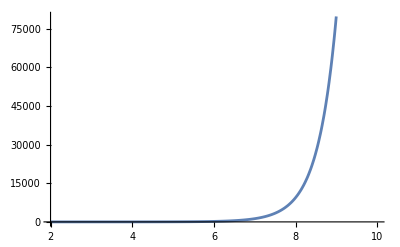

```mathematica
int=NDSolveValue[{f'[x]==Gamma[x+1]/2-Gamma[x-1]/2,f[2]==0},f,{x,2,10}];
Plot[int[x],{x,2,10}]
```

```mathematica
int1=NDSolveValue[{(24 π ((mp3[r]/(4 π r^2))r/10000) r^3+6 mnp3[r]+2 Λ r^3)/(2r(3r-6 mnp3[r]+Λ r^3))-Φ'[r]==0/.Λ->10^-52,Φ[0.001]==0.001},Φ,{r,0,10000}]
```

NDSolveValue::underdet: There are more dependent variables, {mnp3[r],Φ[r]}, than equations, so the system is underdetermined.

NDSolveValue[{(r^3/5000000000000000000000000000000000000000000000000000+6 mnp3[r]+(3 r^2 InterpolatingFunction[…][r])/5000)/(2 r (3 r+r^3/10000000000000000000000000000000000000000000000000000-6 mnp3[r]))-Φ'[r]==0,Φ[0.001]==0.001},Φ,{r,0,10000}]

```mathematica
Plot[int1[r],{r,0,10000}]
```

NDSolveValue::dsvar: 0.204286 cannot be used as a variable.

NDSolveValue::dsvar: 204.286 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
(*Below is when Γ = 1 and K = r/b, plot is for phi*)
```

```mathematica
mnp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m,{r,0.0001,10000}]
```

InterpolatingFunction[…]

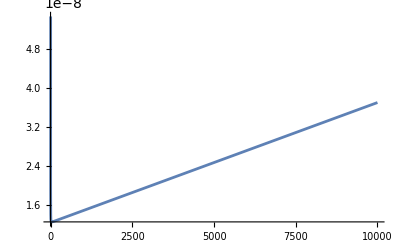

```mathematica
Plot[(24 π ((mp3[r]/(4 π r^2))r/10000) r^3+6 mnp3[r]+2 Λ r^3)/(2r(3r-6 mnp3[r]+Λ r^3))/.Λ->10^-52,{r,0,10000}]
```

# e^(-2Ψ[r])=1-(2m[r])/r+Λr^2/3

```mathematica
(*For K=1 and Γ=1*)
```

```mathematica
m1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m,{r,0.0001,10000}]
```

InterpolatingFunction[…]

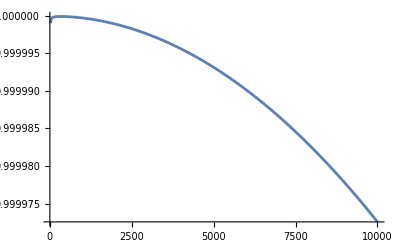

```mathematica
Plot[1-(2m1[r])/r+(Λ r^2)/3/.Λ->10^-52,{r,20,10000}]
```

```mathematica
(*For K=r and Γ=1*)
```

```mathematica
m2=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m,{r,0.0001,9000}]
```

InterpolatingFunction[…]

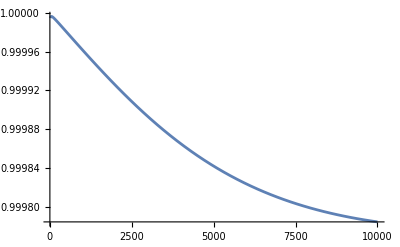

```mathematica
Plot[1-(2m2[r])/r+(Λ r^2)/3/.Λ->10^-52,{r,20,10000}]
```

```mathematica
(*For K= r/band Γ=1*)
```

```mathematica
m3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==10^-5,m[9000]==1},m,{r,0.0001,10000}]
```

NDSolveValue::ndsz: At r == 0.00100003, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::berr: The scaled boundary value residual error of 505.002 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

InterpolatingFunction[…]

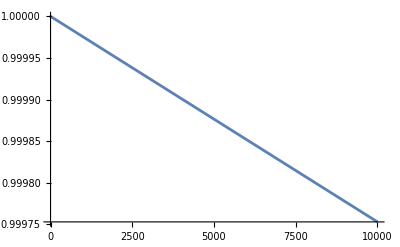

```mathematica
Plot[1-(2m3[r])/r+(Λ r^2)/3/.Λ->10^-52,{r,0.1,10000}]
```

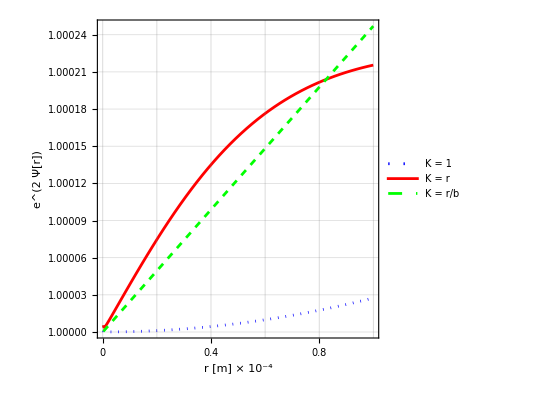

```mathematica
ePSI=Plot[{1/(1-(2m1[r])/r+(Λ r^2)/3)/.Λ->10^-52,1/(1-(2m2[r])/r+(Λ r^2)/3)/.Λ->10^-52,1/(1-(2m3[r])/r+(Λ r^2)/3)/.Λ->10^-52},{r,20,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain]Style["× 10^-4",Plain], Style["e^(2  Ψ[r])",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = 1","K = r","K = r/b"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["ePSI.pdf",ePSI]
```

ePSI.pdf

```mathematica
(*Newtonina grwvitational potential in a way.*)
```

```mathematica
(*Plot analytical version of e^(2Ψ)*)
```

# Analytical Plots

```mathematica
Integrate[4 π r^2(ρ),r]
```

4/3 π r^3 ρ

```mathematica
Integrate[4 π r^2(ρ(1-r/b)),r]
```

4 π (r^3/3-r^4/(4 b)) ρ

```mathematica
Integrate[4 π r^2(ρ(1-r^2/b^2)),r]
```

4 π (r^3/3-r^5/(5 b^2)) ρ

## Spatial Curvature

```mathematica
Plot[(4/3 π r^3 ρ)/r^3+10^-52/3/.ρ->10^-22,{r,0.001,10000}]
```

-Graphics-

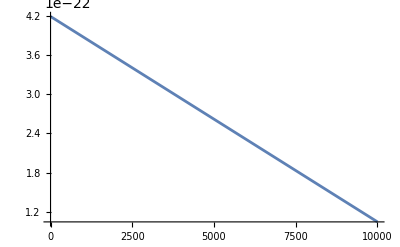

```mathematica
Plot[(4 π (r^3/3-r^4/(4 b)) ρ)/r^3+10^-52/3/.{ρ->10^-22,b->10000},{r,0.001,10000}]
```

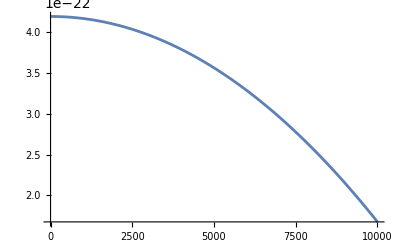

```mathematica
Plot[(4 π (r^3/3-r^5/(5 b^2)) ρ)/r^3+10^-52/3/.{ρ->10^-22,b->10000},{r,0.001,10000}]
```

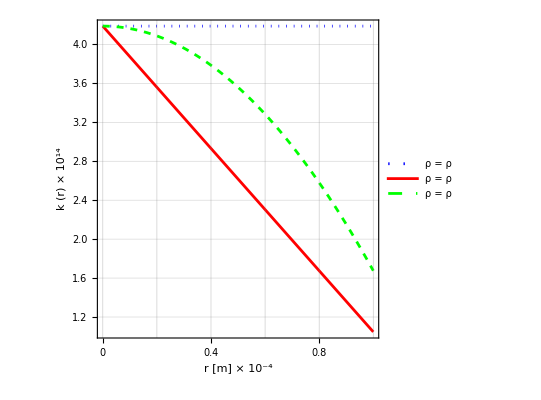

```mathematica
Aspatialcurv=Plot[{((4/3 π r^3 ρ)/r^3+10^-52/3)/10^-22/.ρ->10^-22,((4 π (r^3/3-r^4/(4 b)) ρ)/r^3+10^-52/3)/10^-22/.{ρ->10^-22,b->10000},((4 π (r^3/3-r^5/(5 b^2)) ρ)/r^3+10^-52/3)/10^-22/.{ρ->10^-22,b->10000}},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "k"Style["(r)",Plain]  Style["× 10^14",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Bottom}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["Aspatialcurv.pdf",Aspatialcurv]
```

Aspatialcurv.pdf

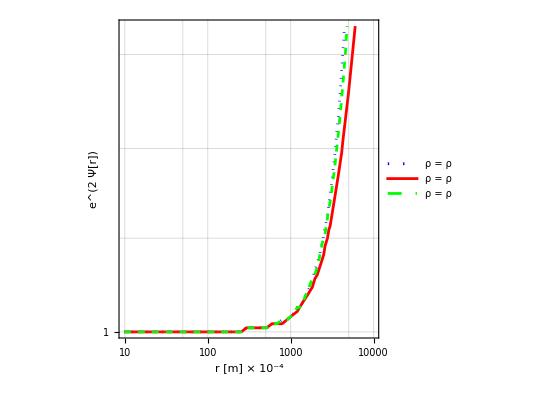

```mathematica
AePSI=LogLogPlot[{1/(1-(2(4/3 π r^3 ρ))/r+(Λ r^2)/3)/.{Λ->10^-52,ρ->10^-22},1/(1-(2(4 π (r^3/3-r^4/(4 b)) ρ))/r+(Λ r^2)/3)/.{Λ->10^-52,ρ->10^-22,b->10000},1/(1-(2(4 π (r^3/3-r^5/(5 b^2)) ρ))/r+(Λ r^2)/3)/.{Λ->10^-52,ρ->10^-22,b->10000}},{r,0,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain]Style["× 10^-4",Plain], Style["e^(2  Ψ[r])",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["AePSI.pdf",AePSI]
```

AePSI.pdf